```mathematica
Quit[];
```

```mathematica
(* This notebook practices plotting WKB curves, the plots are not exactly flawless but a good *)
```

## Theory

```mathematica
(* This note book considers trajectories of the quadratic differential 

ϕ= f(z) dz^2,

  or in other words the flow equation,

d_t z = E^(i θ)/Sqrt[f[z]]

 or in otherwords curves of 

ω = \int_{z_0}^z Sqrt[f[z]]dz 

obeying $Im E^(-I θ) ω=0$  *)
```

```mathematica
(* Turning points will be shown in purple and pole points in Orange *)
```

## Stokes Diagram Technology

```mathematica
(* NOTE ALWAYS USE z as the coordinate *)

(* Find turning points within a range *)
 TuringPoints[f_,Range_]:=Module[{tpsols},
tpsols= NSolve[f[z]==0&&Abs[z]<Range,z];
If[tpsols=={},{}, DeleteDuplicates[Chop[z/.tpsols]]]];

(* Find emmission directions from a turning point *)
Raydirections[f_,θ_,ztp_]:=χ/.NSolve[ComplexExpand[Im[  Sqrt[D[f[z],z]/.z-> ztp]E^(-I θ + I χ 3/ 2)]]==0&&0≤χ<2π,χ]

(* Create some seed points a small radius δ from a given turning points *)
Rayseeder1tp[f_,θ_,ztp_,δ_]:= Module[{raydirs, rayseedcomplex,rayseedxy}, 
raydirs= Raydirections[f,θ,ztp];
rayseedcomplex=Table[ ztp+δ E^(I raydirs[[i]]),{i, 1, Dimensions[raydirs][[1]]}];
rayseedxy =Table[{Re[rayseedcomplex[[i]]]  ,Im[rayseedcomplex[[i]]]},{i, 1, Dimensions[rayseedcomplex][[1]]}]] 

(* Compile this over all turning points *)
Rayseederall[f_,θ_,tpset_,δ_]:= Module[{dimtps, seed1},
dimtps= Dimensions[tpset][[1]];  
Do[seed1[i] = Rayseeder1tp[f,θ,tpset[[i]],δ],{i,1 ,dimtps}];
Table[seed1[i],{i,1 ,dimtps}]] 

(* Find poles  within a range *)
Poles[f_,Range_]:=Module[{polessols},
polessols= NSolve[1/(f[z])==0&&Abs[z]<Range,z];
If[polessols=={},{}, DeleteDuplicates[z/.polessols]]
];

(* Find the real flow equations  *)
RePar[eqs_]:=eqs/Sqrt[eqs[[1]]^2+eqs[[2]]^2]
Floweq[f_, θ_]:={ ComplexExpand[Re[E^(I θ)/Sqrt[f[x + I y  ]]]], ComplexExpand[Im[E^(I θ)/Sqrt[f[x + I y  ]]]]};

(* PlotFlow, introducing a small displacement so as to miss the seed point *)
FlowPlot[f_, θ_,xRange_ ,yRange_,cut_,Detail_,Colour_:Red]:= Module[{eqs,turingpoints,turingpointsxy,polepoints,polepointsxy, seedsnearturningpoints}, 
StartTime=AbsoluteTime[];

(*Gather ingredients*)
eqs= FullSimplify[RePar[Evaluate[Floweq[f, θ]]]];
turingpoints= TuringPoints[f,Sqrt[xRange^2+yRange^2]];
turingpointsxy=Table[{Re[turingpoints[[i]]]  ,Im[turingpoints[[i]]]},{i, 1, Dimensions[turingpoints][[1]]}]; 
polepoints=Poles[f,Sqrt[xRange^2+yRange^2]];
polepointsxy=If[ polepoints=={},{},Table[{Re[polepoints[[i]]]  ,Im[polepoints[[i]]]},{i, 1, Dimensions[polepoints][[1]]}]]; 
seedsnearturningpoints=Flatten[ Rayseederall[f,θ,turingpoints ,cut],1];
Print["Check: all info ready"];

(*Create plots*)
SeedLines=
StreamPlot[eqs,{x,-xRange,xRange},{y,-yRange,yRange},StreamPoints->{ seedsnearturningpoints },StreamScale->  {Full,All},PerformanceGoal->"Speed", StreamStyle-> Colour  ] ;
 
BackgroundLines=StreamPlot[eqs,{x,-xRange,xRange},{y,-yRange,yRange},StreamPoints->Automatic, StreamStyle-> LightGray,StreamScale-> Full,PerformanceGoal->"Speed" ] ;

TurningPointsPlot=ListPlot[turingpointsxy,PlotRange->{ {-xRange,xRange}, {-yRange,yRange}},PlotStyle->Directive[PointSize[Large],Purple]];

PolePointsPlot=ListPlot[polepointsxy,PlotRange->{ {-xRange,xRange}, {-yRange,yRange}},PlotStyle->Directive[PointSize[Large],Orange]];

EndTime=AbsoluteTime[];
Print["The computation took " <>ToString[UnitConvert[Quantity[EndTime-StartTime,"Seconds"],MixedUnit[{"Minutes", "Seconds"}]]]];

out = Show[SeedLines, BackgroundLines, TurningPointsPlot, PolePointsPlot]
]
```

## Some Nice Examples From 1401.7094 Iwaki and Nakanishi

```mathematica
(*Load up a library of nice interesting functions as in figure 3 of 1401.7094 *)
fa[z_]:=  z;
fb[z_]:= z(z+1)(z+I);
fc[z_]:= z(z+2)/((z-1)^2(z-2I)^2);
fd[z_]:= E^(I π/10)(1-z^2);
fe[z_]:=   (1-z^2);
ff[z_]:= E^(-I π/10)(1-z^2);
fg[z_]:=  - E^(π I /20)(z+2 I)(z-3 I)/z^2;
fh[z_]:=  -(z+2 I)(z-3 I)/z^2;
fi[z_]:=  - E^(-π I /20)(z+2 I)(z-3 I)/z^2;
```

```mathematica
(*FlowPlot[f_, θ_,xRange_ ,yRange_,cut_,Detail_,Colour_]*)
```

Check: all info ready

The computation took 0 minutes 0.2423842 seconds

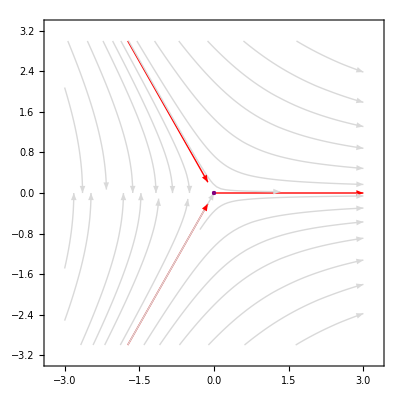

```mathematica
FlowPlot[fa,0,3,3,0.3,Fine]
```

```mathematica
η=0.2;
ζ=0.4;
m=4η ζ/ (1+ (η+ζ)^2);
energy=0.1;
fv[z_]:=JacobiSN[z, m]^2(1+(ζ-η)JacobiSN[z, m]^2)/JacobiDN[z,m]^2-energy
```

```mathematica
FlowPlot[fv,0,4,5,0.1,Automatic]
```

Check: all info ready

```mathematica
θ=0;
cut=0.1;
xRange=4;
yRange=3;
Detail =Fine;
turingpoints= TuringPoints[fv,Sqrt[xRange^2+yRange^2]];
turingpointsxy=Table[{Re[turingpoints[[i]]]  ,Im[turingpoints[[i]]]},{i, 1, Dimensions[turingpoints][[1]]}]; 
polepoints=Poles[fv,Max[xRange,yRange]];
polepointsxy=If[ polepoints=={},{},Table[{Re[polepoints[[i]]]  ,Im[polepoints[[i]]]},{i, 1, Dimensions[polepoints][[1]]}]]; 
seedsnearturningpoints=Flatten[ Rayseederall[fv,θ,turingpoints ,cut],1];
eqs= FullSimplify[RePar[Evaluate[Floweq[fv, θ]]]];
```

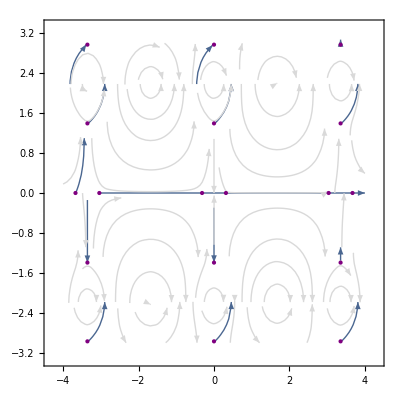

```mathematica
SeedLines=
StreamPlot[eqs,{x,-xRange,xRange},{y,-yRange,yRange},StreamPoints->{ seedsnearturningpoints },StreamScale->  {Full,All},PerformanceGoal->"Speed", StreamStyle-> Colour  ] ;
 
BackgroundLines=StreamPlot[eqs,{x,-xRange,xRange},{y,-yRange,yRange},StreamPoints->Automatic, StreamStyle-> LightGray,StreamScale-> Full,PerformanceGoal->"Speed" ] ;

TurningPointsPlot=ListPlot[turingpointsxy,PlotRange->{ {-xRange,xRange}, {-yRange,yRange}},PlotStyle->Directive[PointSize[Large],Purple]];

PolePointsPlot=ListPlot[polepointsxy,PlotRange->{ {-xRange,xRange}, {-yRange,yRange}},PlotStyle->Directive[PointSize[Large],Orange]];

out = Show[SeedLines, BackgroundLines, TurningPointsPlot, PolePointsPlot]
```

```mathematica
(*Create plots*)
SeedLines=
StreamPlot[eqs,{x,-xRange,xRange},{y,-yRange,yRange},StreamPoints->{ seedsnearturningpoints },StreamScale->  {Full,All},PerformanceGoal->"Speed" ] ;
```

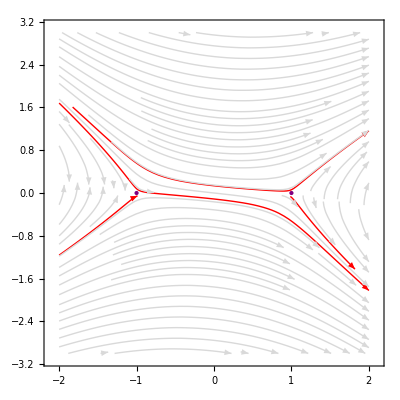
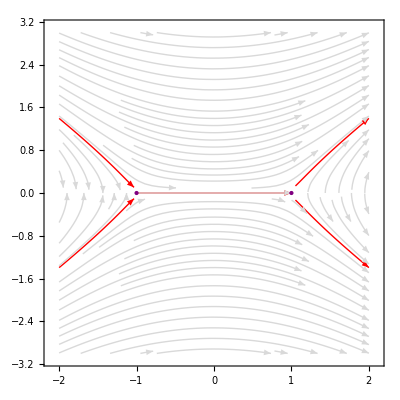
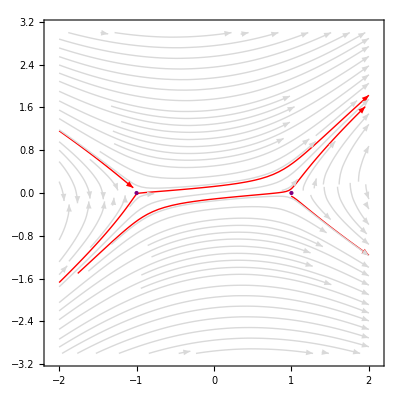

```mathematica
{FlowPlot[fd,0,2,3,0.4,Fine,Red],FlowPlot[fe,0,2,3,0.4,Fine,Red],FlowPlot[ff,0,2,3,0.4,Fine,Red]}
```

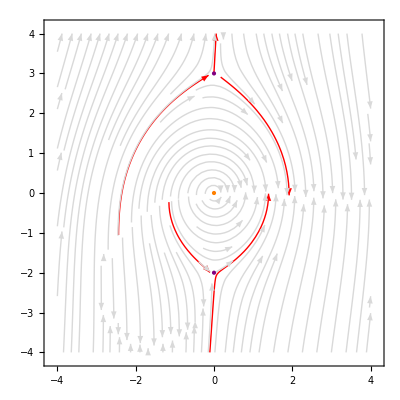
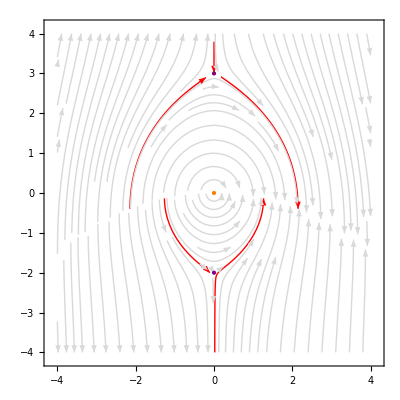
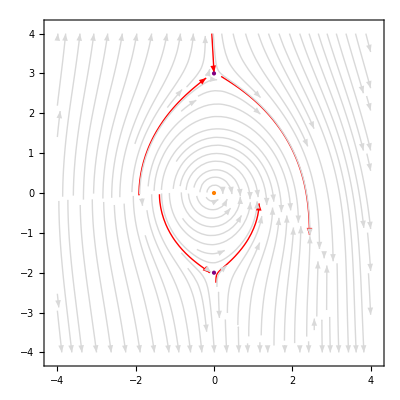

```mathematica
{FlowPlot[fg,0,4,0.4,Fine],FlowPlot[fh,0,4,0.4,Fine],FlowPlot[fi,0,4,0.4,Fine]}
```

## Examples From 1504.08324 Pure N=2 SYM and Exact WKB (Kashani-Poor and Troost)

```mathematica
(*FlowPlot[f_, θ_, Range_ ,cut_,Detail_]*)
```

```mathematica
(* Note that the angle θ in this work book is negative of that of 1504.08324*)
```

```mathematica
fMathieu[u_][z_]:= Cos[z]-u;
```

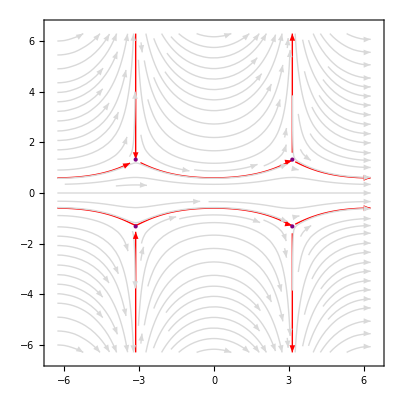
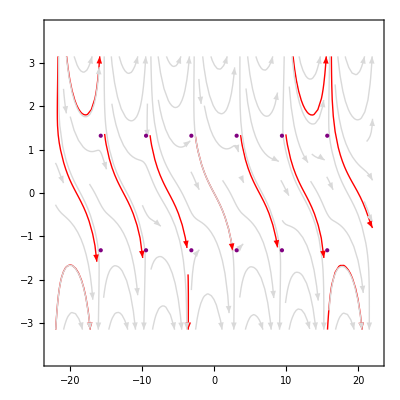
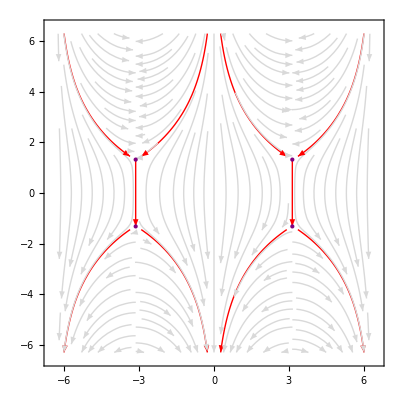

```mathematica
{FlowPlot[fMathieu[-2],0,2π,2π,0.35,Fine,Red] ,FlowPlot[fMathieu[-2],-0.301659, 7π,π,0.001,Fine,Red],FlowPlot[fMathieu[-2],-π/2,2π,2π,0.3,Fine,Red] }
```

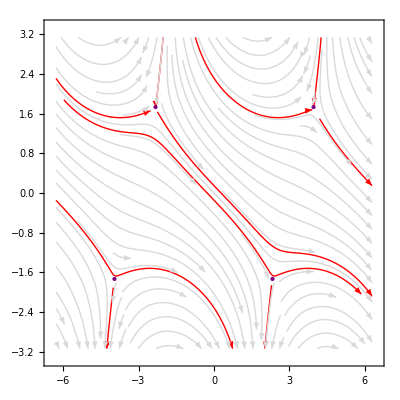
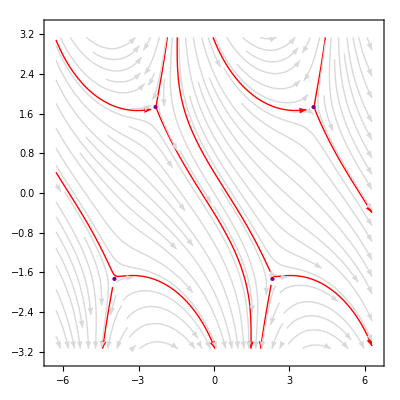

```mathematica
{FlowPlot[fMathieu[-2 +2 I],- π/4,2π,π,0.4,Fine,Red],FlowPlot[fMathieu[-2+2 I],-5π/16,2π,π,0.4,Fine,Red]}
```

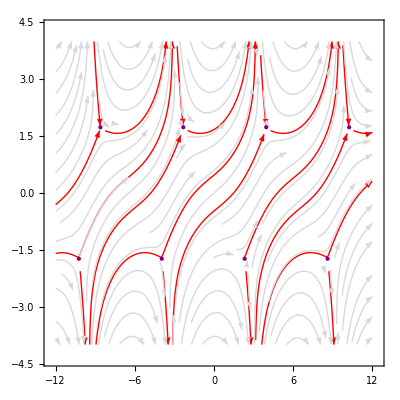

```mathematica
FlowPlot[fMathieu[-2 +2 I],0,12,4,0.4,Fine,Red]
```

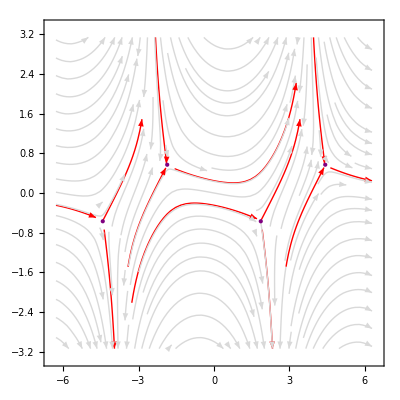
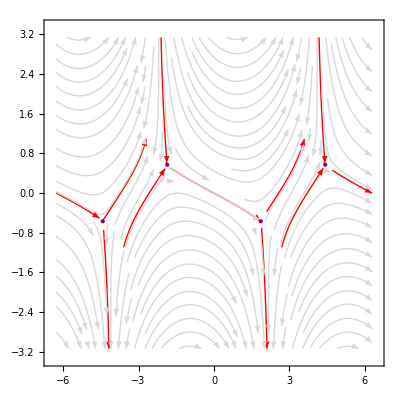
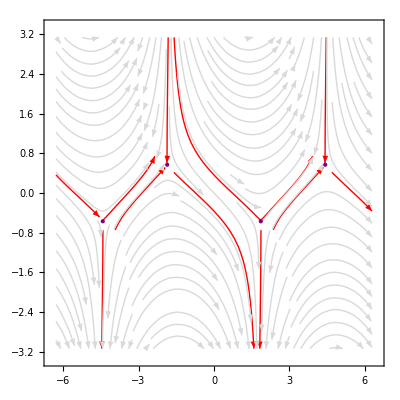

```mathematica
(* figure 6 *)
{FlowPlot[fMathieu[2/3 E^(2 I π/3)],-0.3,2π,π,0.4,Fine,Red],FlowPlot[fMathieu[2/3 E^(2 I π/3)],-0.47,2π,π,0.4,Fine,Red],FlowPlot[fMathieu[2/3 E^(2 I π/3)],-0.69,2π,π,0.4,Fine,Red]}
```

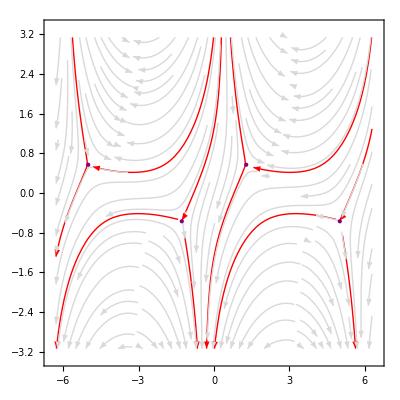
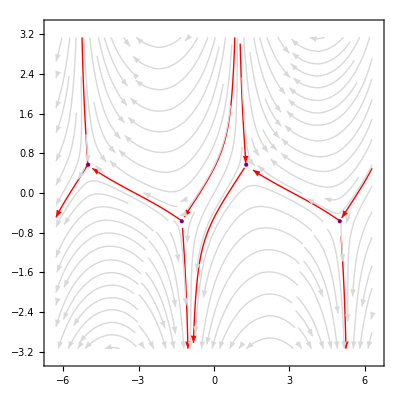
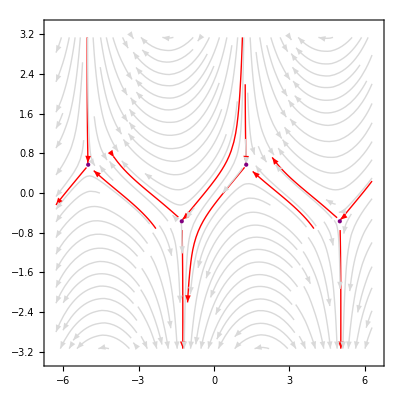

```mathematica
(* figure 6bis *)
{FlowPlot[fMathieu[2/3 E^(- I π/3)],-1.75,2π,π,0.4,Fine,Red],FlowPlot[fMathieu[2/3 E^(- I π/3)],-2.04,2π,π,0.4,Fine,Red],FlowPlot[fMathieu[2/3 E^(- I π/3)],-2.2,2π,π,0.4,Fine,Red]}
```

## Examples From η-deformed Theory

#### Technology

```mathematica
(* This constructs the expected stokes rays in the θt -- the phase of the Borel angle === negative the phase of g^2 *)
SFF[η_]:=2 (1+(η+η^(-1))ArcTan[η]);
SCF[η_]:=  (1-(η+η^(-1))ArcCot[η]);
SFFray[η_]:= ParametricPlot[ {r Cos[Arg[SFF[η]]],r Sin[Arg[SFF[η]]]},{r,0,5},PlotRange-> {{-5,5},{-5,5}} ,PlotStyle-> Red] ;
SCFray[η_]:= ParametricPlot[ {r Cos[Arg[SCF[η]]],r Sin[Arg[SCF[η]]]},{r,0,5},PlotRange-> {{-5,5},{-5,5}},PlotStyle-> Green] ;
SCFraybar[η_]:= ParametricPlot[ {r Cos[-Arg[SCF[η]]],r Sin[-Arg[SCF[η]]]},{r,0,5},PlotRange-> {{-5,5},{-5,5}},PlotStyle-> {Green,Dashed}] ;
RayPlot[η_]:= Show[{SFFray[η],SCFray[η],SCFraybar[η]}];
θRay[θ_]:=  ParametricPlot[{r Cos[θ],r Sin[θ]} ,{r,0,5},PlotRange-> {{-5,5},{-5,5}} ,PlotStyle->{ Black }] ;
```

```mathematica
(* Two Forms for the quadratic differential for the η-deformed theory *)
fWH[η_,ℰ1_][z_]:= Sin[z]^2+η^2 Sin[z]^4- ℰ1;
fη[η_,ℰ_][z_]:=1/8(4 -8 ℰ  +3  η^2-4   (1+η^2) Cos[2 z]+  η^2 Cos[4 z]);
Simplify[fWH[η,ℰ][z]-  fη[η,ℰ][z]]
```

0

#### PLOTS FOR PAPER

```mathematica
(* Case for η Real *)
```

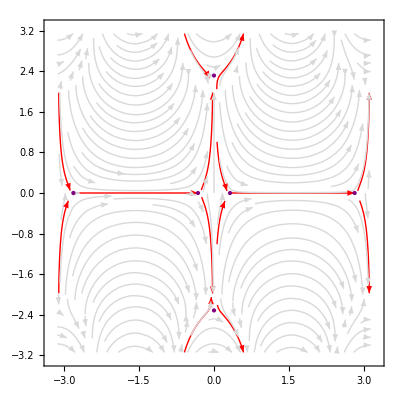

```mathematica
FlowPlot[fη[0.2 , 0.1  ], 0, π,π,0.25,Fine, Red ]
```

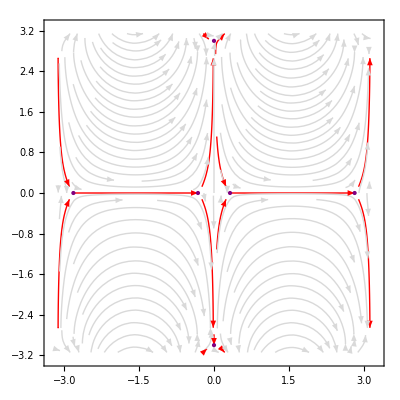
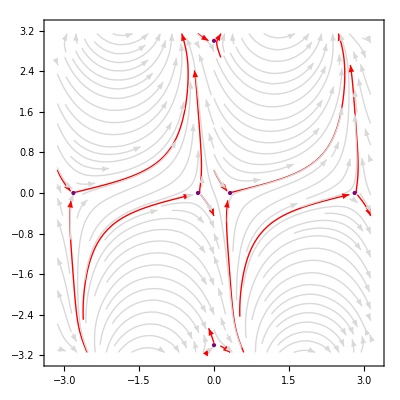
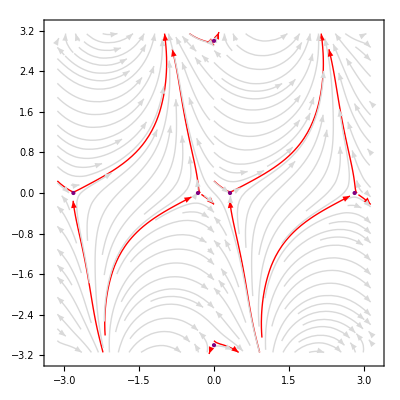
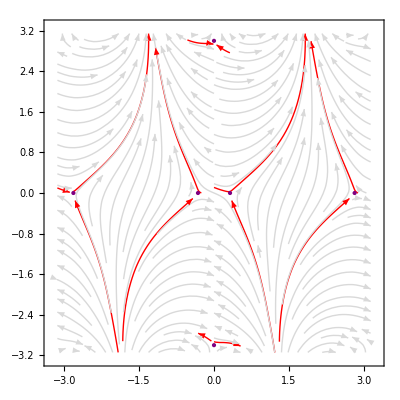
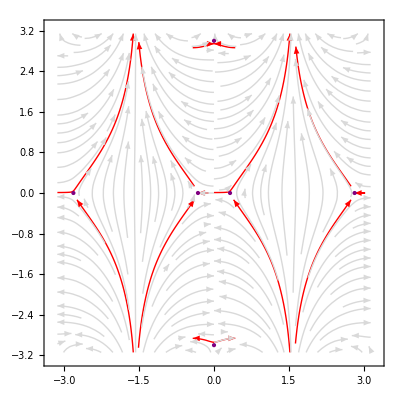
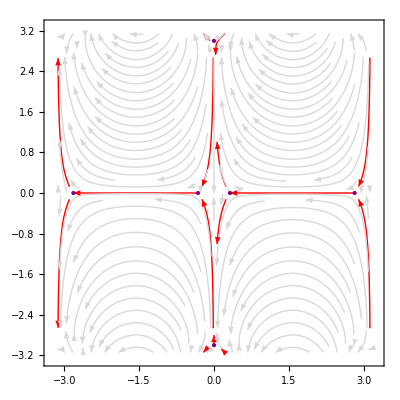

```mathematica
(*η= 0.1 , E=0.1 *){FlowPlot[fη[0.1 , 0.1], 0, π,π,0.2,Fine, Red ],FlowPlot[fη[0.1 , 0.1], π/8, π,π,0.2,Fine, Red ],FlowPlot[fη[0.1 , 0.1], π/4, π,π,0.2,Fine, Red ],FlowPlot[fη[0.1 , 0.1], 3π/8, π,π,0.2,Fine, Red ],FlowPlot[fη[0.1 , 0.1], π/2, π,π,0.2,Fine, Red ],FlowPlot[fη[0.1 , 0.1], π, π,π,0.2,Fine, Red ]}
```

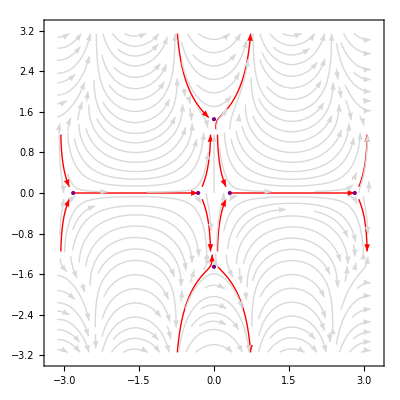
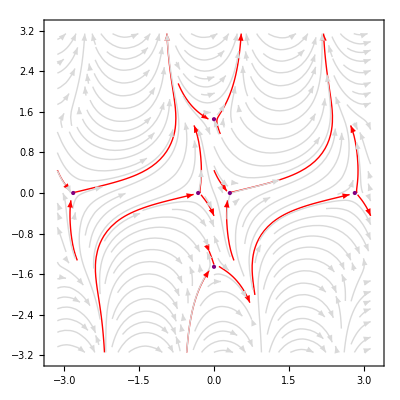
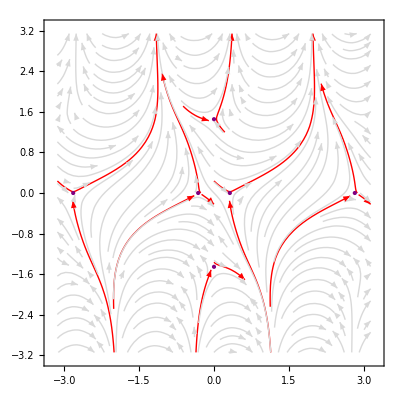
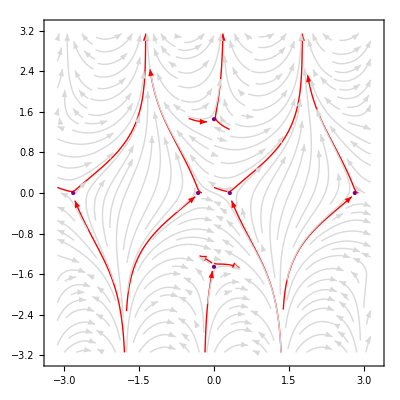
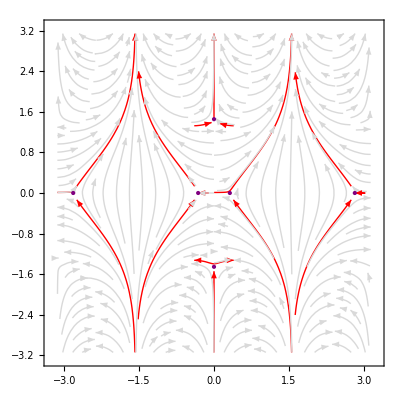
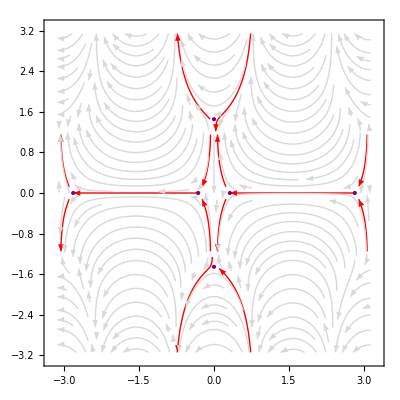

```mathematica
(*η= 0.5, E=0.1  *){FlowPlot[fη[0.5 , 0.1], 0, π,π,0.2,Fine, Red ],FlowPlot[fη[0.5 , 0.1], π/8, π,π,0.2,Fine, Red ],FlowPlot[fη[0.5 , 0.1], π/4, π,π,0.2,Fine, Red ],FlowPlot[fη[0.5 , 0.1], 3π/8, π,π,0.2,Fine, Red ],FlowPlot[fη[0.5 , 0.1], π/2, π,π,0.2,Fine, Red ],FlowPlot[fη[0.5 , 0.1], π, π,π,0.2,Fine, Red ]}
```

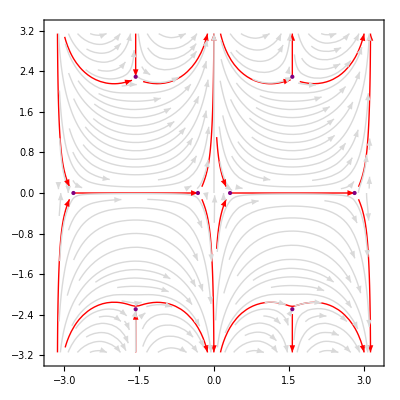
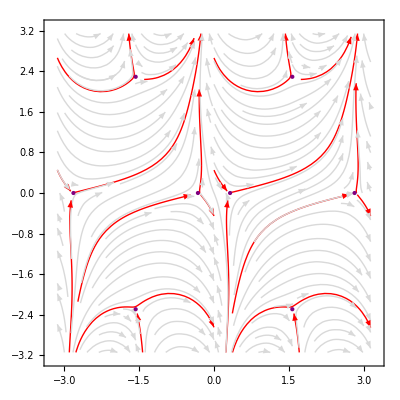
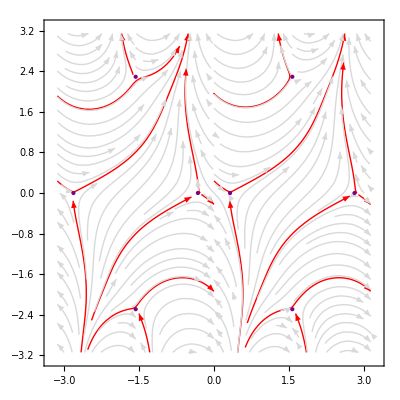
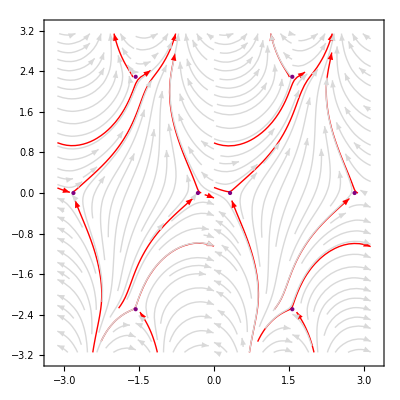
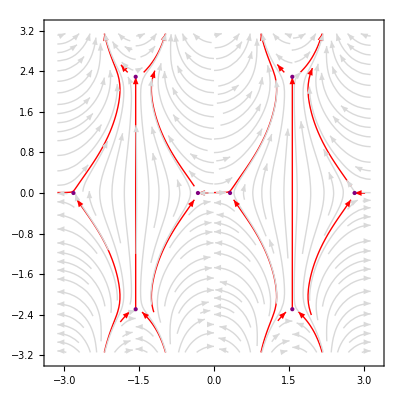
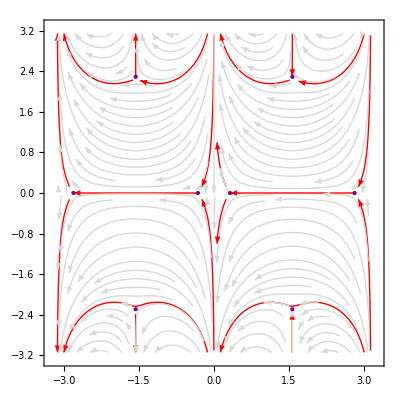

```mathematica
(*η= I/5 , E=0.1  *){FlowPlot[fη[I/5 , 0.1], 0, π,π,0.2,Fine, Red ],FlowPlot[fη[I/5, 0.1], π/8, π,π,0.2,Fine, Red ],FlowPlot[fη[I/5 , 0.1], π/4, π,π,0.2,Fine, Red ],FlowPlot[fη[I/5, 0.1], 3π/8, π,π,0.2,Fine, Red ],FlowPlot[fη[I/5 , 0.1], π/2, π,π,0.2,Fine, Red ],FlowPlot[fη[I/5 , 0.1], π, π,π,0.2,Fine, Red ]}
```

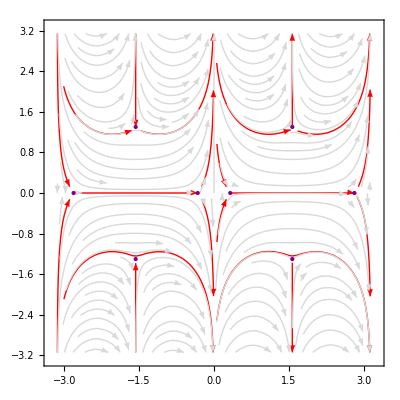
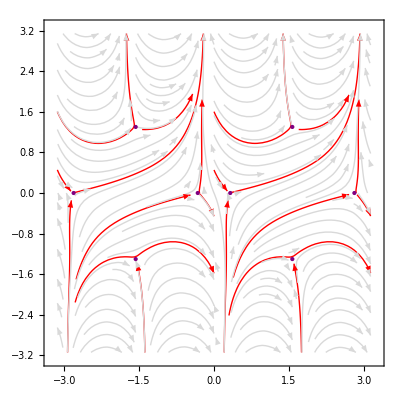
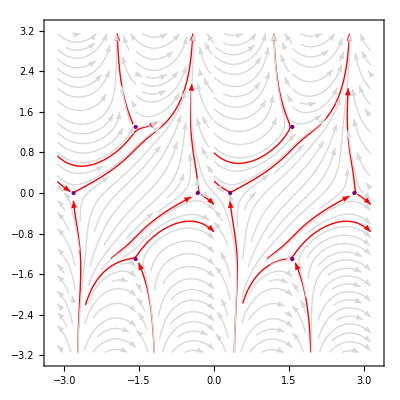
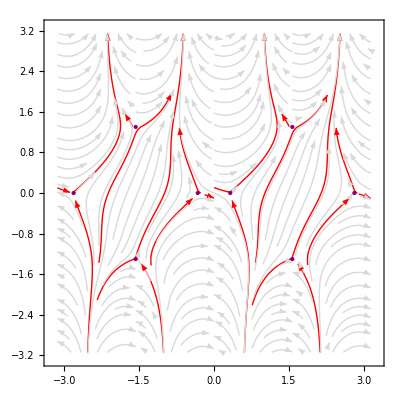
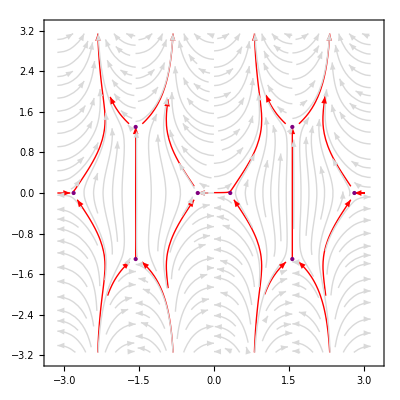
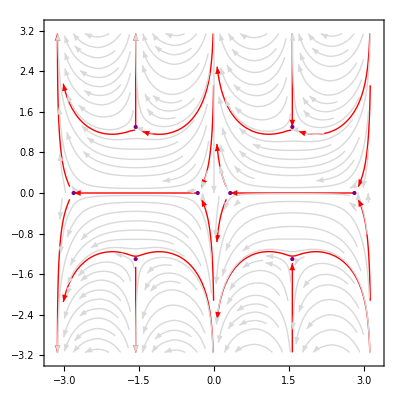

```mathematica
(*η= I/2 , E=0.1  *){FlowPlot[fη[I/2 , 0.1], 0, π,π,0.2,Fine, Red ],FlowPlot[fη[I/2 , 0.1], π/8, π,π,0.2,Fine, Red ],FlowPlot[fη[I/2 , 0.1], π/4, π,π,0.2,Fine, Red ],FlowPlot[fη[I/2 , 0.1], 3π/8, π,π,0.2,Fine, Red ],FlowPlot[fη[I/2 , 0.1], π/2, π,π,0.2,Fine, Red ],FlowPlot[fη[I/2 , 0.1], π, π,π,0.2,Fine, Red ]}
```

```mathematica
SFFR[ηR_]:= 2( 1-(ηR- ηR^(-1))ArcTanh[ηR]);
SCFR[ηR_]:=( 1-(ηR- ηR^(-1))ArcTanh[ηR])+ I π/2(ηR- ηR^(-1));
SCFRbar[ηR_]:=( 1-(ηR- ηR^(-1))ArcTanh[ηR])- I π/2(ηR- ηR^(-1));
```

```mathematica
θFFR[ηR_]:= Arg[SFFR[ηR]];
θCFR[ηR_]:= Arg[SCFR[ηR]];
θCFRbar[ηR_]:= Arg[SCFRbar[ηR]];
```

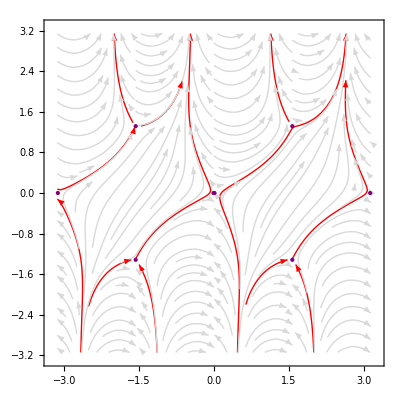

```mathematica
FlowPlot[fη[I/2 , 0.0001], θCFRbar[1/2] , π,π,0.14,Fine, Red ]
```

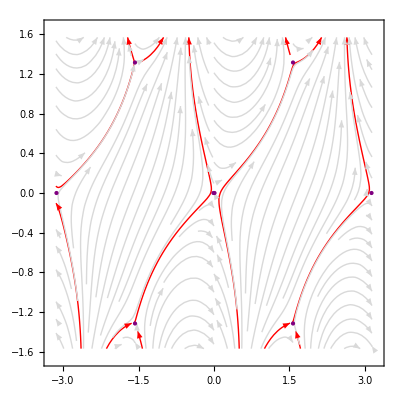

```mathematica
FlowPlot[fη[I/2 , 0.0001], θCFRbar[1/2] , π,π/2,0.12,Fine, Red ]
```

#### PLOTS FOR PAPER

```mathematica
(* Plots the Stokes Diagram for a given Energy, eta, and Stokes phase*) 
PlotStokesandRays[η_,ℰ_, θ_]:= {FlowPlot[fη[η , ℰ], -θ/2, π,π,0.2,Fine, Red ],Show[RayPlot[η],θRay[θ] ]}
```

```mathematica
(* Seeds some values for θt including the special ones asociated to saddles *) θVals[η_]:=  DeleteDuplicates[Sort[N[Mod[Sort[Join[Table[ II π/10, {II,0,22}], {Arg[SFF[η]],Arg[SCF[η]],-Arg[SCF[η]]}]] ,2π]]]];
```

```mathematica
(* Builds a bunch of plots for various values of θ.  We set E=1, the leading behaviour  *) 
MovFrames[η_]:= Table[PlotStokesandRays[η,1,θVals[η] [[jj]]],{jj,1,Dimensions[θVals[η]][[1]]}] ;
```

#### η Real

```mathematica
(* First the Real Cases *)
η0pt001= MovFrames[0.001];
η0pt25= MovFrames[0.25];
η0pt5= MovFrames[0.5];
```

```mathematica
ListAnimate[η0pt001]
```

```mathematica
ListAnimate[η0pt25]
```

```mathematica
ListAnimate[η0pt5]
```

NOTE IN THIS TEXT: θ is θt the phase of the Borel Plane parameter.  It is negative twice that used for the stokes plots 

So indeed we see the occurence of topology jumps as we pass through both the θ=0 and θ=π as expected.  Notice that even for the Mathieu equation, for which we have only the real uniton solution with finite action contributing to the resurgent structure, the Stokes diagram does a jump at θ=π.  These diagrams probably know then about all sorts of semi-classical solutions, even ones that have zero Stokes mulitplier on a given integration thimble.

We can also see that there are some other finite Stokes Lines entering the picture at intermediate values of θ.  For η very large we see that this occurs at θt= n π/4.

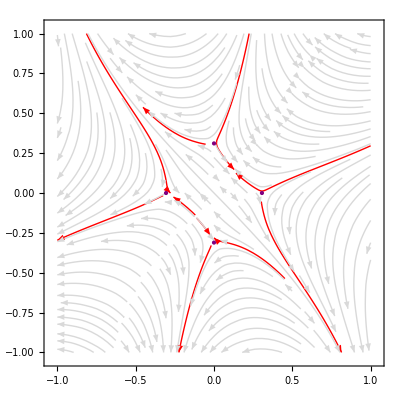

```mathematica
FlowPlot[fη[10.5, 1],- 3π/4, 1,1,0.08,Fine, Red]
```

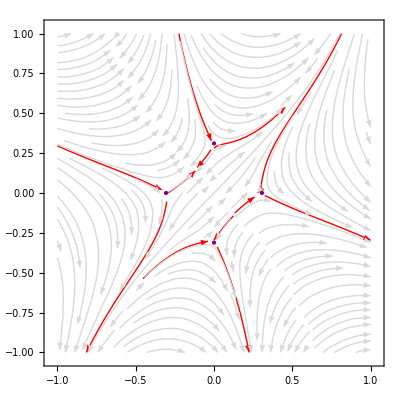

```mathematica
FlowPlot[fη[10.5, 1],- π/4, 1,1,0.08,Fine, Red]
```

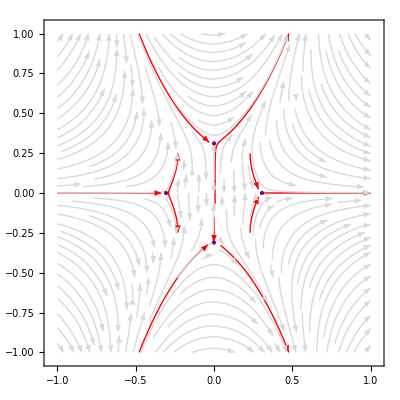

```mathematica
FlowPlot[fη[10.5, 1], 0, 1,1,0.08,Fine, Red]
```

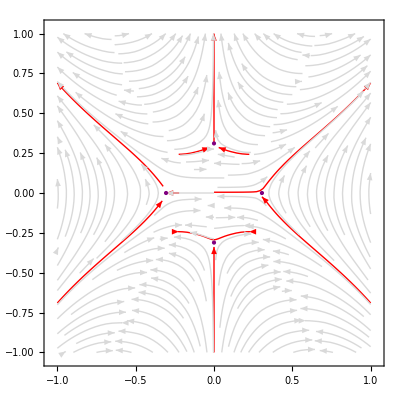

```mathematica
FlowPlot[fη[10.5, 1], π/2, 1,1,0.08,Fine, Red]
```

From eyballing the diagram θ=- 3π/4(1+x) we have a very rough look at how the eta dependence

```mathematica
Data={{0.25,1.22},{0.35,1.18},{0.45,1.155},{0.5,1.147},{0.6, 1.13},{0.7,1.11},{1,1.08},{1.5,1.058},{2.5,1.041},{3.5,1.025},{4.5,1.021},{5.5,1.014}};(* Eyeball guess as to where the stokes jump is *)
```

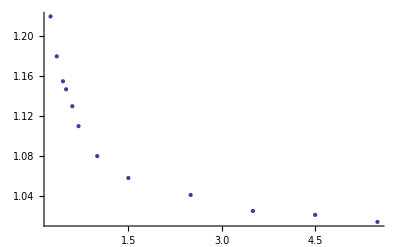

```mathematica
ListPlot[Data]
```

```mathematica
(* Cases Imag *) 
η0pt25i= MovFrames[0.25I];
```

```mathematica
ListAnimate[η0pt25i]
```

```mathematica
ListAnimate[η0pt75i]
```

#### η Pure Imaginary

```mathematica
(* η= I ηR *)
```

```mathematica
SFFR[ηR_]:= 2( 1-(ηR- ηR^(-1))ArcTanh[ηR]);
SCFR[ηR_]:=( 1-(ηR- ηR^(-1))ArcTanh[ηR])+ I π/2(ηR- ηR^(-1));
SCFRbar[ηR_]:=( 1-(ηR- ηR^(-1))ArcTanh[ηR])- I π/2(ηR- ηR^(-1));
```

```mathematica
θFFR[ηR_]:= Arg[SFFR[ηR]];
θCFR[ηR_]:= Arg[SCFR[ηR]];
θCFRbar[ηR_]:= Arg[SCFRbar[ηR]];
```

We see a stokes line at θ=0

```mathematica
E^(I π/2)
```

ⅈ

```mathematica
θFFR[ηR]
```

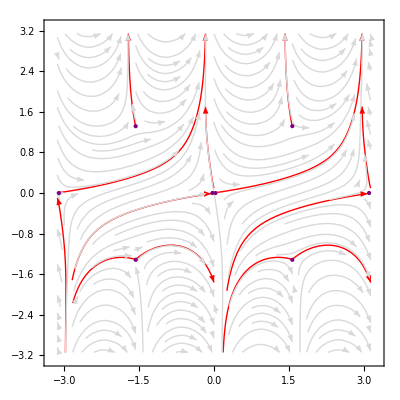

```mathematica
FlowPlot[ fη[I 0.5 , 0.001], π/10 , π,π,0.1,Fine, Red ]
```

```mathematica
StokesPlots[ηR_,ℰ_]:= {FlowPlot[fη[I ηR , ℰ],θFFR[ηR] , π,π,0.2,Fine, Red ],FlowPlot[fη[I ηR , ℰ],θCFRbar[ηR] , π,π,0.2,Fine, Red ],FlowPlot[fη[I ηR , ℰ],π /2 , π,π,0.2,Fine, Red ],FlowPlot[fη[I ηR , ℰ],θCFR[ηR] , π,π,0.2,Fine, Red ]};
```

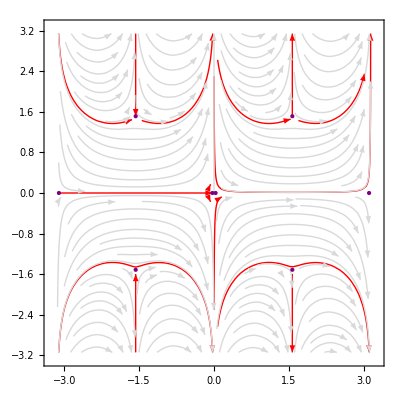
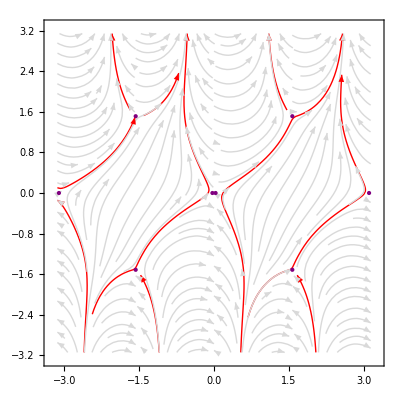
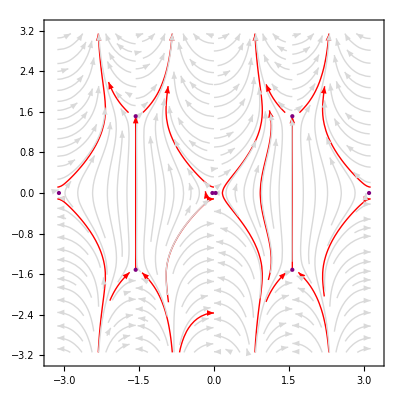
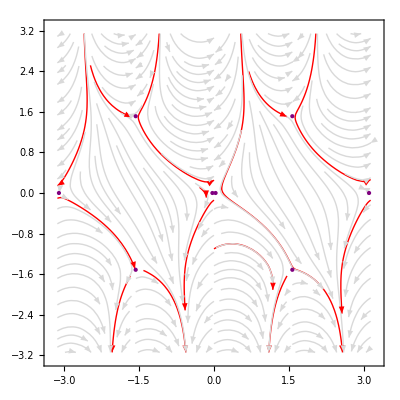

```mathematica
StokesPlots[0.42,0.001]
```

#### η Complex Number Arg[η]<π/2

```mathematica
θFF[η_]:= Arg[SFF[η]];
θCF[η_]:= Arg[SCF[η]];
θCFbar[η_]:=- Arg[SCF[η]];
```

```mathematica
StokesPlotsηComplex[η_,ℰ_]:= {FlowPlot[fη[ η , ℰ],0 , π,2,0.2,Fine, Red ],FlowPlot[fη[ η , ℰ],θFF[η] , π,2,0.2,Fine, Red ], FlowPlot[fη[ η , ℰ],θCF[η] , π,2,0.2,Fine, Red ]};
```

```mathematica
ηfig10= N[Exp[I π/5]/2];
```

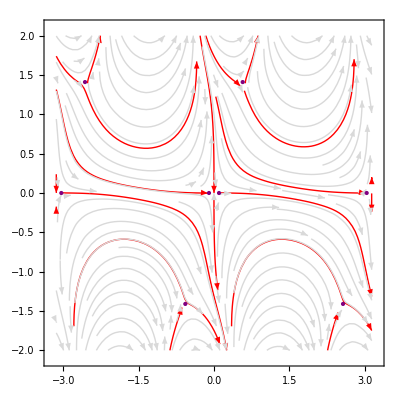
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
StokesPlotsηComplex[ηfig10,0.01](* So we see that θ=0 (left) is not on the money, bu θ=Arg[SFF] (middel) is!  As is θ= Arf[SCF] (Right)!  *)
```

```mathematica
(* Seeds some values for θt including the special ones asociated to saddles *) θVals[η_]:=  DeleteDuplicates[Sort[N[Sort[Mod[Join[Table[ II π/20, {II,0,40}],{θFF[η],θCF[η],-θFF[η],-θCF[η]}],2π]]]]];
```

```mathematica
movdata[η_]:=Table[FlowPlot[fη[ η , 0.01],θVals[η][[jj]] , π,2,0.2,Fine, Red ],{jj,1,Dimensions[θVals[η]][[1]]}] ;
```

```mathematica
mve=movdata[ηfig10];
Export["test2.mov", mve, "VideoEncoding"-> "MPEG-4 Video", "FrameRate"-> 4]
```

test2.mov

```mathematica
SetDirectory["/Users/danielthompson/Dropbox"]
```

/Users/danielthompson/Dropbox

test.mov

```mathematica
ηfig10bis= N[ Exp[I π/5]];
StokesPlotsηComplex[ηfig10bis,0.01]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
ηfig10bisbis= N[ Exp[2 I π/5]];
StokesPlotsηComplex[ηfig10bisbis,0.01]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{FlowPlot[fη[2I/Sqrt[2] , 0.01], 0, π,π,0.2,Fine, Red ],FlowPlot[fη[2I/Sqrt[2] , 0.01], π/8, π,π,0.2,Fine, Red ],FlowPlot[fη[2I/Sqrt[2], 0.01], π/4, π,π,0.2,Fine, Red ],FlowPlot[fη[2I/Sqrt[2], 0.01], 3π/8, π,π,0.2,Fine, Red ],FlowPlot[fη[2I/Sqrt[2], 0.01], π/2, π,π,0.2,Fine, Red ],FlowPlot[fη[2I/Sqrt[2] , 0.01], π, π,π,0.2,Fine, Red ]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListAnimate[Table[FlowPlot[fη[I ϵ , 0.01], 3π/8, 2π,2π,0.2,Fine, Red ],{ϵ,0,2,0.1}]]
```

## Double Deformed Theory

```mathematica
m[ζ_,η_]:=4ζ η/(1+(ζ+η)^2)
fηζ[η_,ζ_,ϵ_][z_]:=ϵ+(JacobiSN[z, m[ζ,η]]^2 (1+(η-ζ)^2JacobiSN[z, m[ζ,η]]^2))/JacobiDN[z, m[ζ,η]]^2
fseries[η_,ζ_,ϵ_][z_]:=Evaluate[Normal[Series[fηζ[η,ζ,ϵ][z], {z, 0, 20}]]];
```

### Single Deformation

```mathematica
FlowPlot[fηζ[0.2,0,0.1], Pi/8,π+0.2, π, 0.25, Fine, Red]
FlowPlot[fηζ[0.2,0,0.1], 0,π+0.2, π, 0.25, Fine, Red]
FlowPlot[fηζ[0.2,0,0.1], -Pi/8,π+0.4, π, 0.25, Fine, Red]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
FlowPlot[fηζ[0.2,0,0.1], Pi/8,π+0.2, π, 0.25, Fine, Red]
FlowPlot[fseries[0.2,0,0.1], 0,π+0.2, π, 0.25, Fine, Red]
FlowPlot[fseries[0.2,0,0.1], -Pi/8,π+0.4, π, 0.25, Fine, Red]
```

-Graphics-

-Graphics-

-Graphics-

### Double Deformation

```mathematica
FlowPlot[fηζ[0.2,0.4,0.1], Pi/8,π+0.4, π, 0.25, Medium, Red]
```

$Aborted

```mathematica
FlowPlot[fηζ[0.2,0.4,0.1], Pi/8,π+0.4, π, 0.25, Fine, Red]
FlowPlot[fηζ[0.2,0.4,0.1], 0,π+0.4, π, 0.25, Fine, Red]
FlowPlot[fηζ[0.2,0.4,0.1], -Pi/8,π+0.4, π, 0.25, Fine, Red]
```

$Aborted

$Aborted

$Aborted

### Critical Point

```mathematica
FlowPlot[fηζ[0.4,0.4,0.1], Pi/8,π+0.4, π, 0.25, Fine, Red]
FlowPlot[fηζ[0.4,0.4,0.1], 0,π+0.4, π, 0.25, Fine, Red]
FlowPlot[fηζ[0.4,0.4,0.1], -Pi/8,π+0.4, π, 0.25, Fine, Red]
```

### Approach Critical Point

#### θ = 0

```mathematica
FlowPlot[fηζ[0.2,0.4,0.1], 0,π+0.4, π, 0.25, Fine, Red]
FlowPlot[fηζ[0.35,0.4,0.1], 0,π+0.4, π, 0.25, Fine, Red]
FlowPlot[fηζ[0.39,0.4,0.1], 0,π+0.4, π, 0.25, Fine, Red]
FlowPlot[fηζ[0.4,0.4,0.1], 0,π+0.4, π, 0.25, Fine, Red]
```

#### θ positive

```mathematica
FlowPlot[fηζ[0.2,0.4,0.1], Pi/8,π+0.4, π, 0.25, Fine, Red]
FlowPlot[fηζ[0.35,0.4,0.1], Pi/8,π+0.4, π, 0.25, Fine, Red]
FlowPlot[fηζ[0.39,0.4,0.1], Pi/8,π+0.4, π, 0.25, Fine, Red]
FlowPlot[fηζ[0.4,0.4,0.1], Pi/8,π+0.4, π, 0.25, Fine, Red]
```